```mathematica
FindBarelyPartitions[vertexCount_,colorCount_:4]:=Block[{types=IntegerPartitions[vertexCount,{colorCount}]},
PrintTemporary[{vertexCount,Length[types]}];
Tally[
Monitor[
Flatten[ParallelTable[BroaderTypes[t],
{t,types}
],1],t]]
]
```

```mathematica
FindBarelyPartitions[6]
```

{{{3,1,1,1},1},{{2,1,1,1,1},2},{{1,1,1,1,1,1},2},{{2,2,1,1},1}}

```mathematica
BroaderTypes[type_]:=Block[{result={type},pos, current,new,parts,pos2,currentpart,previous=-1,newpart},
For[pos=1,pos<=Length[type],pos++,
current=type[[pos]];
If[current≠1 && current ≠ previous,
new=Drop[type,{pos}];
parts=IntegerPartitions[current];
For[pos2=1,pos2≤Length[parts],pos2++,
currentpart=parts[[pos2]];
newpart=ReverseSort[Join[new,currentpart]];
AppendTo[result,newpart]
]
];
previous=current
];
DeleteDuplicates[result]
]
```

```mathematica
BroaderTypes[type_]:=Block[{result={type},first,new,parts,pos2,currentpart,previous=-1,newpart},
first=type[[1]];
If[first==1,
result
,
new=Rest[type];
parts=IntegerPartitions[first,{2,first}];
For[pos2=1,pos2≤Length[parts],pos2++,
currentpart=parts[[pos2]];
newpart=ReverseSort[Join[new,currentpart]];
result=Join[result,BroaderTypes[newpart]]
];
];
DeleteDuplicates[result]
]
```

```mathematica
BroaderTypes[type_]:=BroaderTypes[type,{}]
```

```mathematica
BroaderTypes[type_,result_]:=Block[{pos,current,parts, partpos,new,currentPart,newPart,result2=result},
If[MemberQ[result2,type],
result2
,
AppendTo[result2,type];
For[pos=1,pos<=Length[type],pos++,
current=type[[pos]];
If[current≠1,
parts=IntegerPartitions[current,{2}];
new=Drop[type,{pos}];
For[partpos=1,partpos<=Length[parts],partpos++,
currentPart=parts[[partpos]];
newPart=ReverseSort[Join[new,currentPart]];
result2=BroaderTypes[newPart,result2]
]
]
];
result2
]
]
```

```mathematica
BroaderTypes[{5,2,1}]//Length
```

11

```mathematica
VertexInComponent[PartitionTypeLattice[IntegerPartitions[8]],{{5,2,1}}]//Length
```

11

```mathematica
With[{g=PartitionTypeLattice[IntegerPartitions[8]]},
Table[{Length[VertexInComponent[PartitionTypeLattice[IntegerPartitions[8]],{v}]],Length[BroaderTypes[v]]},{v,VertexList[g]}]
]
```

{{15,15},{22,22},{17,17},{15,15},{14,14},{11,11},{11,11},{11,11},{11,11},{9,9},{7,7},{8,8},{6,6},{7,7},{5,5},{5,5},{5,5},{4,4},{3,3},{3,3},{2,2},{1,1}}

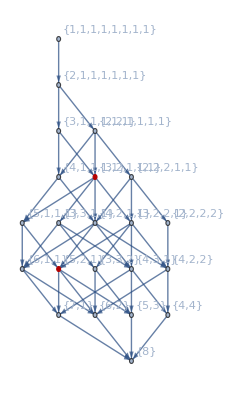

```mathematica
Graph[PartitionTypeLattice[IntegerPartitions[8]],GraphLayout->"LayeredDigraphEmbedding", VertexLabels->"Name", GraphHighlight->{{5,2,1},ConjugatePartition[{5,2,1}]}]
```

```mathematica
FindBarelyPartitions[6]
```

{{{3,1,1,1},1},{{2,1,1,1,1},2},{{1,1,1,1,1,1},1},{{2,2,1,1},1}}

```mathematica
FindBarelyPartitions[8]
```

{{5,1,1,1},{4,1,1,1,1},{3,1,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{2,2,1,1,1,1},{3,2,1,1,1}}

{{4,2,1,1},{3,2,1,1,1},{2,2,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{2,2,2,1,1}}

{{3,3,1,1},{3,2,1,1,1},{2,2,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{3,1,1,1,1,1}}

{{3,2,2,1},{2,2,2,1,1},{2,2,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}

{{2,2,2,2},{2,2,2,1,1},{2,2,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}

{{{5,1,1,1},1},{{4,1,1,1,1},1},{{3,1,1,1,1,1},2},{{2,1,1,1,1,1,1},5},{{1,1,1,1,1,1,1,1},5},{{2,2,1,1,1,1},5},{{3,2,1,1,1},3},{{4,2,1,1},1},{{2,2,2,1,1},3},{{3,3,1,1},1},{{3,2,2,1},1},{{2,2,2,2},1}}

```mathematica
Always[n_]:=Always[n]=CalcAlways[FindBarelyPartitions[n]]
```

```mathematica
Always[4]
```

{{1,1,1,1}}

```mathematica
Always[5]
```

{{2,1,1,1},{1,1,1,1,1}}

```mathematica
Always[9]
```

{{2,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1},{2,2,1,1,1,1,1},{2,2,2,1,1,1}}

```mathematica
FindBarelyPartitions[9]
```

{{{6,1,1,1},1},{{5,1,1,1,1},1},{{4,1,1,1,1,1},1},{{3,1,1,1,1,1,1},2},{{2,1,1,1,1,1,1,1},6},{{1,1,1,1,1,1,1,1,1},6},{{2,2,1,1,1,1,1},6},{{3,2,1,1,1,1},4},{{4,2,1,1,1},2},{{2,2,2,1,1,1},6},{{3,3,1,1,1},2},{{5,2,1,1},1},{{3,2,2,1,1},4},{{4,3,1,1},1},{{4,2,2,1},1},{{2,2,2,2,1},2},{{3,3,2,1},1},{{3,2,2,2},1}}

```mathematica
WhatsNew[n_]:=Block[{previous=Always[n-1],current=Always[n]},
previous=Map[Append[#,1]&,previous];
Select[current,!MemberQ[previous,#]&]
]
```

```mathematica
Monitor[TableForm[Table[{k,Length[Always[k]]},{k,3,40}],TableHeadings->{ {},{"N","#"}},TableDepth->2],k]
```

$Aborted

```mathematica
Monitor[TableForm[Table[{k,Length[Always[k]],FactorInteger[1+Length[Always[k]]]},{k,3,35}],TableHeadings->{ {},{"N","#"}},TableDepth->2],k]
```

| N | # | 
 | 3 | 0 | {{1,1}}
 | 4 | 1 | {{2,1}}
 | 5 | 2 | {{3,1}}
 | 6 | 2 | {{3,1}}
 | 7 | 3 | {{2,2}}
 | 8 | 3 | {{2,2}}
 | 9 | 6 | {{7,1}}
 | 10 | 7 | {{2,3}}
 | 11 | 8 | {{3,2}}
 | 12 | 11 | {{2,2},{3,1}}
 | 13 | 19 | {{2,2},{5,1}}
 | 14 | 21 | {{2,1},{11,1}}
 | 15 | 26 | {{3,3}}
 | 16 | 31 | {{2,5}}
 | 17 | 52 | {{53,1}}
 | 18 | 66 | {{67,1}}
 | 19 | 76 | {{7,1},{11,1}}
 | 20 | 88 | {{89,1}}
 | 21 | 134 | {{3,3},{5,1}}
 | 22 | 169 | {{2,1},{5,1},{17,1}}
 | 23 | 215 | {{2,3},{3,3}}
 | 24 | 251 | {{2,2},{3,2},{7,1}}
 | 25 | 358 | {{359,1}}
 | 26 | 412 | {{7,1},{59,1}}
 | 27 | 517 | {{2,1},{7,1},{37,1}}
 | 28 | 639 | {{2,7},{5,1}}
 | 29 | 899 | {{2,2},{3,2},{5,2}}
 | 30 | 1065 | {{2,1},{13,1},{41,1}}
 | 31 | 1242 | {{11,1},{113,1}}
 | 32 | 1496 | {{3,1},{499,1}}
 | 33 | 2072 | {{3,1},{691,1}}
 | 34 | 2482 | {{13,1},{191,1}}
 | 35 | 2930 | {{3,1},{977,1}}

```mathematica
Always[4]
```

{{1,1,1,1}}

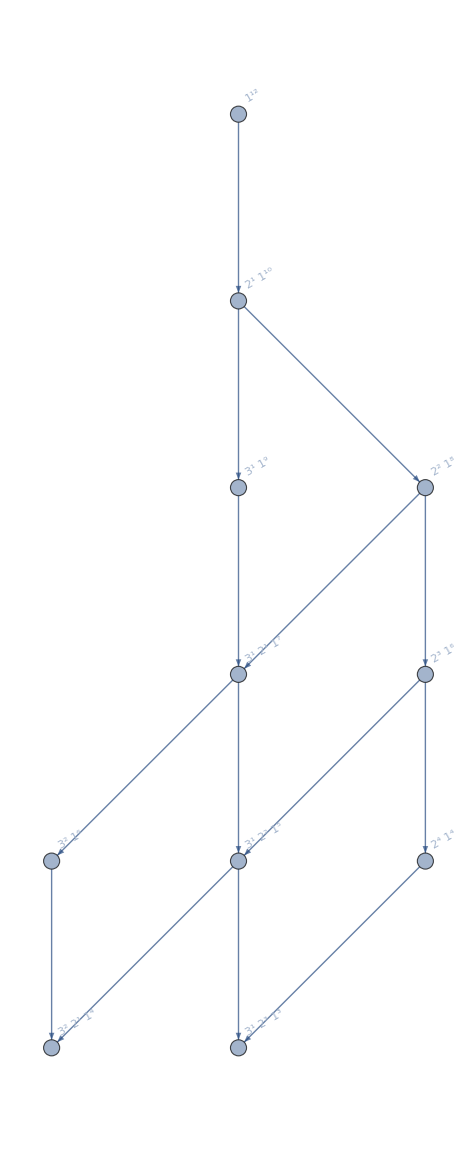

```mathematica
With[{g=PartitionTypeLattice[Always[12]]},Graph[g,GraphLayout->"LayeredDigraphEmbedding",VertexLabels->Map[#->Rotate[Framed[ExponentNotation[#]],Pi/6]&,VertexList[Graph[g]]]]]
```

```mathematica
ConjugatePartition[{5,4,2}]
```

{3,3,2,2,1}

```mathematica
TableForm[Table[{k,Length[Always[k]],Framed[Column[Sort[Map[ExponentNotation,Always[k]]]]],Map[Length,Always[k]]},{k,3,17}],TableHeadings->{ {},{"N","#","new","@rank"}},TableDepth->2]
```

| N | # | new | @rank
 | 3 | 0 |  | {}
 | 4 | 1 | 1^4 | {4}
 | 5 | 2 | 1^5
2^1 1^3 | {4,5}
 | 6 | 2 | 1^6
2^1 1^4 | {5,6}
 | 7 | 3 | 1^7
2^1 1^5
2^2 1^3 | {6,7,5}
 | 8 | 3 | 1^8
2^1 1^6
2^2 1^4 | {7,8,6}
 | 9 | 6 | 1^9
2^1 1^7
2^2 1^5
2^3 1^3
3^1 1^6
3^1 2^1 1^4 | {7,8,9,7,6,6}
 | 10 | 7 | 1^10
2^1 1^8
2^2 1^6
2^3 1^4
3^1 1^7
3^1 2^1 1^5
3^1 2^2 1^3 | {8,9,10,8,7,7,6}
 | 11 | 8 | 1^11
2^1 1^9
2^2 1^7
2^3 1^5
2^4 1^3
3^1 1^8
3^1 2^1 1^6
3^1 2^2 1^4 | {9,10,11,9,8,8,7,7}
 | 12 | 11 | 1^12
2^1 1^10
2^2 1^8
2^3 1^6
2^4 1^4
3^1 1^9
3^2 1^6
3^1 2^1 1^7
3^1 2^2 1^5
3^1 2^3 1^3
3^2 2^1 1^4 | {10,11,12,10,9,9,8,8,8,7,7}
 | 13 | 19 | 1^13
2^1 1^11
2^2 1^9
2^3 1^7
2^4 1^5
2^5 1^3
3^1 1^10
3^2 1^7
4^1 1^9
3^1 2^1 1^8
3^1 2^2 1^6
3^1 2^3 1^4
3^2 2^1 1^5
3^2 2^2 1^3
4^1 2^1 1^7
4^1 2^2 1^5
4^1 2^3 1^3
4^1 3^1 1^6
4^1 3^1 2^1 1^4 | {10,11,12,13,11,10,9,10,9,9,8,8,9,8,8,7,7,8,7}
 | 14 | 21 | 1^14
2^1 1^12
2^2 1^10
2^3 1^8
2^4 1^6
2^5 1^4
3^1 1^11
3^2 1^8
4^1 1^10
3^1 2^1 1^9
3^1 2^2 1^7
3^1 2^3 1^5
3^1 2^4 1^3
3^2 2^1 1^6
3^2 2^2 1^4
4^1 2^1 1^8
4^1 2^2 1^6
4^1 2^3 1^4
4^1 3^1 1^7
4^1 3^1 2^1 1^5
4^1 3^1 2^2 1^3 | {11,12,13,14,12,11,10,11,10,10,9,9,10,9,9,8,8,9,8,8,7}
 | 15 | 26 | 1^15
2^1 1^13
2^2 1^11
2^3 1^9
2^4 1^7
2^5 1^5
2^6 1^3
3^1 1^12
3^2 1^9
3^3 1^6
4^1 1^11
3^1 2^1 1^10
3^1 2^2 1^8
3^1 2^3 1^6
3^1 2^4 1^4
3^2 2^1 1^7
3^2 2^2 1^5
3^2 2^3 1^3
3^3 2^1 1^4
4^1 2^1 1^9
4^1 2^2 1^7
4^1 2^3 1^5
4^1 2^4 1^3
4^1 3^1 1^8
4^1 3^1 2^1 1^6
4^1 3^1 2^2 1^4 | {12,13,14,15,13,12,11,12,11,11,10,10,11,10,10,9,9,9,10,9,9,8,8,8,9,8}
 | 16 | 31 | 1^16
2^1 1^14
2^2 1^12
2^3 1^10
2^4 1^8
2^5 1^6
2^6 1^4
3^1 1^13
3^2 1^10
3^3 1^7
4^1 1^12
3^1 2^1 1^11
3^1 2^2 1^9
3^1 2^3 1^7
3^1 2^4 1^5
3^1 2^5 1^3
3^2 2^1 1^8
3^2 2^2 1^6
3^2 2^3 1^4
3^3 2^1 1^5
3^3 2^2 1^3
4^1 2^1 1^10
4^1 2^2 1^8
4^1 2^3 1^6
4^1 2^4 1^4
4^1 3^1 1^9
4^1 3^2 1^6
4^1 3^1 2^1 1^7
4^1 3^1 2^2 1^5
4^1 3^1 2^3 1^3
4^1 3^2 2^1 1^4 | {13,14,15,16,14,13,12,13,12,12,11,11,12,11,11,10,10,10,11,10,9,10,9,9,9,10,9,8,9,8,8}
 | 17 | 52 | 1^17
2^1 1^15
2^2 1^13
2^3 1^11
2^4 1^9
2^5 1^7
2^6 1^5
2^7 1^3
3^1 1^14
3^2 1^11
3^3 1^8
4^1 1^13
4^2 1^9
5^1 1^12
3^1 2^1 1^12
3^1 2^2 1^10
3^1 2^3 1^8
3^1 2^4 1^6
3^1 2^5 1^4
3^2 2^1 1^9
3^2 2^2 1^7
3^2 2^3 1^5
3^2 2^4 1^3
3^3 2^1 1^6
3^3 2^2 1^4
4^1 2^1 1^11
4^1 2^2 1^9
4^1 2^3 1^7
4^1 2^4 1^5
4^1 2^5 1^3
4^1 3^1 1^10
4^1 3^2 1^7
4^2 2^1 1^7
4^2 2^2 1^5
4^2 2^3 1^3
4^2 3^1 1^6
5^1 2^1 1^10
5^1 2^2 1^8
5^1 2^3 1^6
5^1 2^4 1^4
5^1 3^1 1^9
5^1 3^2 1^6
4^1 3^1 2^1 1^8
4^1 3^1 2^2 1^6
4^1 3^1 2^3 1^4
4^1 3^2 2^1 1^5
4^1 3^2 2^2 1^3
4^2 3^1 2^1 1^4
5^1 3^1 2^1 1^7
5^1 3^1 2^2 1^5
5^1 3^1 2^3 1^3
5^1 3^2 2^1 1^4 | {13,14,15,16,17,15,14,13,14,13,12,13,12,12,13,12,11,11,11,12,11,11,11,12,11,10,10,10,10,11,10,10,9,9,10,11,10,9,9,9,9,10,9,9,8,8,9,10,9,8,8,8}

```mathematica
TableForm[Table[{k,Length[WhatsNew[k]],Framed[Column[Sort[Map[ExponentNotation,WhatsNew[k]]]]],Map[Length,WhatsNew[k]]},{k,3,20}],TableHeadings->{ {},{"N","#","new","@rank"}},TableDepth->2]
```

```mathematica
TableForm[Table[{k,Length[WhatsNew[k]],Framed[Column[Sort[Map[ExponentNotation,WhatsNew[k]]]]],Map[Length,WhatsNew[k]]},{k,3,20}],TableHeadings->{ {},{"N","#","new","@rank"}},TableDepth->2]
```

| N | # | new | @rank
 | 3 | 0 |  | {}
 | 4 | 1 | 1^4 | {4}
 | 5 | 1 | 2^1 1^3 | {4}
 | 6 | 0 |  | {}
 | 7 | 1 | 2^2 1^3 | {5}
 | 8 | 0 |  | {}
 | 9 | 3 | 2^3 1^3
3^1 1^6
3^1 2^1 1^4 | {7,6,6}
 | 10 | 1 | 3^1 2^2 1^3 | {6}
 | 11 | 1 | 2^4 1^3 | {7}
 | 12 | 3 | 3^2 1^6
3^1 2^3 1^3
3^2 2^1 1^4 | {8,7,7}
 | 13 | 8 | 2^5 1^3
4^1 1^9
3^2 2^2 1^3
4^1 2^1 1^7
4^1 2^2 1^5
4^1 2^3 1^3
4^1 3^1 1^6
4^1 3^1 2^1 1^4 | {10,9,8,8,7,7,8,7}
 | 14 | 2 | 3^1 2^4 1^3
4^1 3^1 2^2 1^3 | {8,7}
 | 15 | 5 | 2^6 1^3
3^3 1^6
3^2 2^3 1^3
3^3 2^1 1^4
4^1 2^4 1^3 | {9,8,8,9,8}
 | 16 | 5 | 3^1 2^5 1^3
3^3 2^2 1^3
4^1 3^2 1^6
4^1 3^1 2^3 1^3
4^1 3^2 2^1 1^4 | {9,8,9,8,8}
 | 17 | 21 | 2^7 1^3
4^2 1^9
5^1 1^12
3^2 2^4 1^3
4^1 2^5 1^3
4^2 2^1 1^7
4^2 2^2 1^5
4^2 2^3 1^3
4^2 3^1 1^6
5^1 2^1 1^10
5^1 2^2 1^8
5^1 2^3 1^6
5^1 2^4 1^4
5^1 3^1 1^9
5^1 3^2 1^6
4^1 3^2 2^2 1^3
4^2 3^1 2^1 1^4
5^1 3^1 2^1 1^7
5^1 3^1 2^2 1^5
5^1 3^1 2^3 1^3
5^1 3^2 2^1 1^4 | {13,12,11,11,11,10,10,10,9,9,9,9,9,8,8,9,10,9,8,8,8}
 | 18 | 14 | 3^4 1^6
3^1 2^6 1^3
3^3 2^3 1^3
3^4 2^1 1^4
5^1 2^5 1^3
5^1 4^1 1^9
4^1 3^1 2^4 1^3
4^2 3^1 2^2 1^3
5^1 3^2 2^2 1^3
5^1 4^1 2^1 1^7
5^1 4^1 2^2 1^5
5^1 4^1 2^3 1^3
5^1 4^1 3^1 1^6
5^1 4^1 3^1 2^1 1^4 | {11,10,10,9,9,9,8,9,10,9,9,8,8,8}
 | 19 | 10 | 2^8 1^3
3^2 2^5 1^3
3^4 2^2 1^3
4^1 2^6 1^3
4^1 3^3 1^6
4^2 2^4 1^3
4^1 3^2 2^3 1^3
4^1 3^3 2^1 1^4
5^1 3^1 2^4 1^3
5^1 4^1 3^1 2^2 1^3 | {10,9,10,11,10,9,9,9,9,8}
 | 20 | 12 | 3^1 2^7 1^3
3^3 2^4 1^3
4^2 3^2 1^6
5^1 2^6 1^3
5^1 3^3 1^6
4^1 3^1 2^5 1^3
4^1 3^3 2^2 1^3
4^2 3^1 2^3 1^3
4^2 3^2 2^1 1^4
5^1 3^2 2^3 1^3
5^1 3^3 2^1 1^4
5^1 4^1 2^4 1^3 | {10,10,9,9,10,11,10,10,9,9,9,9}

```mathematica
Monitor[
Table[
With [{counts=FindBarelyPartitions[size]},
size->ShowAlwaysSometimesNeverFromCountTable[counts]
],
{size,4,11}
],size]
```

{4→{4 | 01,31 | 0
22 | 02,211 | 03,1111 | 14},5→{5 | 01,41 | 0
32 | 02,311 | 0
221 | 03,2111 | 14,11111 | 15},6→{6 | 01,51 | 0
42 | 0
33 | 02,411 | 0
321 | 0
222 | 03,3111 | 1
2211 | 14,21111 | 25,111111 | 16},7→{7 | 01,61 | 0
52 | 0
43 | 02,511 | 0
421 | 0
331 | 0
322 | 03,4111 | 1
3211 | 1
2221 | 14,31111 | 2
22111 | 35,211111 | 26,1111111 | 17},8→{8 | 01,71 | 0
62 | 0
53 | 0
44 | 02,611 | 0
521 | 0
431 | 0
422 | 0
332 | 03,5111 | 1
4211 | 1
3311 | 1
3221 | 1
2222 | 14,41111 | 2
32111 | 4
22211 | 35,311111 | 2
221111 | 36,2111111 | 27,11111111 | 18},9→{9 | 01,81 | 0
72 | 0
63 | 0
54 | 02,711 | 0
621 | 0
531 | 0
522 | 0
441 | 0
432 | 0
333 | 03,6111 | 1
5211 | 1
4311 | 1
4221 | 1
3321 | 1
3222 | 14,51111 | 2
42111 | 4
33111 | 3
32211 | 5
22221 | 25,411111 | 2
321111 | 4
222111 | 46,3111111 | 2
2211111 | 37,21111111 | 28,111111111 | 19},10→{10 | 01,91 | 0
82 | 0
73 | 0
64 | 0
55 | 02,811 | 0
721 | 0
631 | 0
622 | 0
541 | 0
532 | 0
442 | 0
433 | 03,7111 | 1
6211 | 1
5311 | 1
5221 | 1
4411 | 1
4321 | 1
4222 | 1
3331 | 1
3322 | 14,61111 | 2
52111 | 4
43111 | 4
42211 | 5
33211 | 5
32221 | 4
22222 | 15,511111 | 2
421111 | 4
331111 | 3
322111 | 6
222211 | 36,4111111 | 2
3211111 | 4
2221111 | 47,31111111 | 2
22111111 | 38,211111111 | 29,1111111111 | 110},11→{11 | 01,101 | 0
92 | 0
83 | 0
74 | 0
65 | 02,911 | 0
821 | 0
731 | 0
722 | 0
641 | 0
632 | 0
551 | 0
542 | 0
533 | 0
443 | 03,8111 | 1
7211 | 1
6311 | 1
6221 | 1
5411 | 1
5321 | 1
5222 | 1
4421 | 1
4331 | 1
4322 | 1
3332 | 14,71111 | 2
62111 | 4
53111 | 4
52211 | 5
44111 | 3
43211 | 7
42221 | 4
33311 | 3
33221 | 5
32222 | 25,611111 | 2
521111 | 4
431111 | 4
422111 | 6
332111 | 6
322211 | 6
222221 | 26,5111111 | 2
4211111 | 4
3311111 | 3
3221111 | 6
2222111 | 47,41111111 | 2
32111111 | 4
22211111 | 48,311111111 | 2
221111111 | 39,2111111111 | 210,11111111111 | 111}}